# Name - Vinay Kishor Roll no. - 20201459 Course - B.Sc (H) computer science Newton Raphson method in different forms

## Newton method: By taking parameters as input

x0 = 1

Nmax = 20

epsilon = 1/1000000

f[x] := Cos[x]

f'[x]:=-Sin[x]

In 1th Number of iterations the approximation to root is :1.64209

Estimated error is :0.642093

In 2th Number of iterations the approximation to root is :1.57068

Estimated error is :0.0714173

In 3th Number of iterations the approximation to root is :1.5708

Estimated error is :0.00012105

1.5708

The final approximation of root is :1.5708

Estimated erroe is :5.91305×10^-13

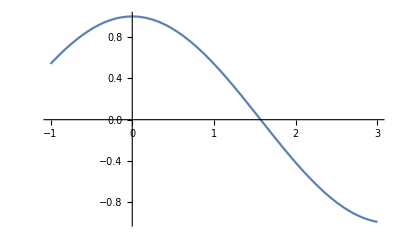

```mathematica
x0 = Input["Enter initial guess :"];
Nmax =Input["Enter maximum number of iterations :"];
eps = Input["Enter a value of convergence parameter :"];
Print["x0 = ",x0];
Print["Nmax = ",Nmax];
Print["epsilon = ",eps];
f[x_] := Cos[x];
Print["f[x] := ",f[x]];
Print["f'[x]:=",D[f[x],x]];
For[i =1, i≤Nmax,i++,x1 = N[x0-(f[x]/.x->x0)/(D[f[x],x]/.x->x0)];
If[Abs[x1-x0]<eps,Return[x1],x0p=x0;x0=x1];
Print["In ",i,
"th Number of iterations the approximation to root is :",x1];
Print["Estimated error is :",Abs[x1-x0p]]];
Print["The final approximation of root is :",x1];
Print["Estimated erroe is :",Abs[x1-x0]];
Plot[f[x],{x,-1,3}]
```

x0 = 0.5

Nmax = 20

epsilon = 1/1000000

f[x] := 1-5 x+x^3

f'[x]:=-5+3 x^2

In 1th Number of iterations the approximation to root is :0.176471

Estimated error is :0.323529

In 2th Number of iterations the approximation to root is :0.201568

Estimated error is :0.0250975

In 3th Number of iterations the approximation to root is :0.20164

Estimated error is :0.0000716007

0.20164

The final approximation of root is :0.20164

Estimated erroe is :6.35602×10^-10

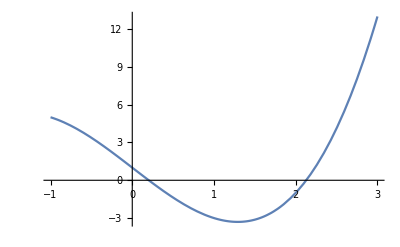

```mathematica
x0 = Input["Enter initial guess :"];
Nmax =Input["Enter maximum number of iterations :"];
eps = Input["Enter a value of convergence parameter :"];
Print["x0 = ",x0];
Print["Nmax = ",Nmax];
Print["epsilon = ",eps];
f[x_] := x^3-5x+1;
Print["f[x] := ",f[x]];
Print["f'[x]:=",D[f[x],x]];
For[i =1, i≤Nmax,i++,x1 = N[x0-(f[x]/.x->x0)/(D[f[x],x]/.x->x0)];
If[Abs[x1-x0]<eps,Return[x1],x0p=x0;x0=x1];
Print["In ",i,
"th Number of iterations the approximation to root is :",x1];
Print["Estimated error is :",Abs[x1-x0p]]];
Print["The final approximation of root is :",x1];
Print["Estimated erroe is :",Abs[x1-x0]];
Plot[f[x],{x,-1,3}]
```

x0 = 1.5

Nmax = 20

epsilon = 1/1000000

f[x] := -ⅇ^x x+Cos[x]

f'[x]:=-ⅇ^x-ⅇ^x x-Sin[x]

In 1th Number of iterations the approximation to root is :0.954848

Estimated error is :0.545152

In 2th Number of iterations the approximation to root is :0.632019

Estimated error is :0.322829

In 3th Number of iterations the approximation to root is :0.527616

Estimated error is :0.104403

In 4th Number of iterations the approximation to root is :0.517838

Estimated error is :0.00977784

In 5th Number of iterations the approximation to root is :0.517757

Estimated error is :0.0000806043

0.517757

The final approximation of root is :0.517757

Estimated erroe is :5.44033×10^-9

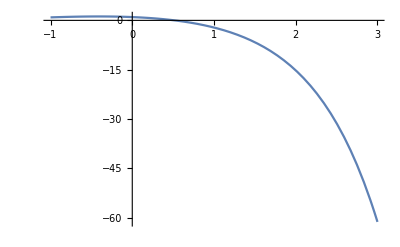

```mathematica
x0 = Input["Enter initial guess :"];
Nmax =Input["Enter maximum number of iterations :"];
eps = Input["Enter a value of convergence parameter :"];
Print["x0 = ",x0];
Print["Nmax = ",Nmax];
Print["epsilon = ",eps];
f[x_] := Cos[x]-x*Exp[x];
Print["f[x] := ",f[x]];
Print["f'[x]:=",D[f[x],x]];
For[i =1, i≤Nmax,i++,x1 = N[x0-(f[x]/.x->x0)/(D[f[x],x]/.x->x0)];
If[Abs[x1-x0]<eps,Return[x1],x0p=x0;x0=x1];
Print["In ",i,
"th Number of iterations the approximation to root is :",x1];
Print["Estimated error is :",Abs[x1-x0p]]];
Print["The final approximation of root is :",x1];
Print["Estimated erroe is :",Abs[x1-x0]];
Plot[f[x],{x,-1,3}]
```